# NLIT (Not-LIT) 9/9/21

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5,1.5};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-5);
dH=1;
```

```mathematica
ImgSize=900;
hbarc=197.32858;
mn=938.3;
hbarsqO2m=hbarc^2/(2 mn);
αfine=1./137.;
hat[l_]:=Sqrt[2 l+1];

resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/results";

files=FileNames[All,resultsDir];
anzBas=Length[Select[files,StringMatchQ[#,"*mat*BasNR*"]&]]/Length[Subscript[I, n]];

tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir];
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"];
Print["Read FORTRAN results from \n",Style[resultsDir,18,Red],"\nin\n",Style[dt,18,Red],"=",Style[datatype,18,Red],"\nformat for\nN_bases=",Style[anzBas,18,Red],"\nevolved bases for the expansion of the final state."];
```

Read FORTRAN results from 
/home/kirscher/kette_repo/ComptonLIT/systems/results
in
float64=Real64
format for
N_bases=21
evolved bases for the expansion of the final state.

#### Orthonormalization of the basis

the function matSqrts obtains transformation matrices to a basis whose elements correspond to the
1) orthogonal Eigenvectors of the original Norm matrix
2) barring those EVs whose Eigenvalues are smaller than the chosen threshold

```mathematica
Clear[normreg,matSqrts];

matSqrts[norm_,cutoff_:0]:=Block[{μ,transf,evs,ovsqi,ovsq,n},

{μ,transf}=Transpose[Select[Sort[Transpose[Eigensystem[norm]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
evs=Eigenvalues[norm];
Print["min/max: ",MinMax[evs]];
n=Length[Select[evs,#<cutoff&]];
Print["(min/max) discarded elements: ",n," ",MinMax[Select[evs,#<cutoff&]]];
Print["elements < 0: ",Length[Select[evs,#<0.&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@evs];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@evs];
(*{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}*)

trafma=(Transpose[transf].DiagonalMatrix[μ^(1/2)]);
invtrafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
evm=(Transpose[invtrafma].norm).invtrafma;
evm=(evm+Transpose[evm])/2;(* symmetrize for stability *)
evv=Eigenvalues[evm];
Print["MinMax[Re] = ",MinMax[Re[evv]]];
Print["MinMax[Im] = ",MinMax[Im[evv]]];
(*Print[ArrayRules[SparseArray[evm]]];*)

{trafma,invtrafma}];

normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the initial state, i.e., J^π=(1/2)^+ for the helion

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
tmp=He3NormHamMat[[Range[1,Length[He3NormHamMat],2]]];
ActiveBasVHe3=ReadList["./Ssigbasv3heLIT_npp0.5^+.dat"];

BareDims=Table[ReadList["./BareBasDims_"<>ToString[nn]<>".dat"],{nn,Range[anzBas]-1}]
(*He3NormHamMat=tmp;*)
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]];
Print["N_(helion - full) = ",He3BasisDim];
Print["N_(helion - active) = ",Length[ActiveBasVHe3]];
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}][[;;;;dH,;;;;dH]];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}][[;;;;dH,;;;;dH]];
MinMax[Eigenvalues[He3Norm]]
```

{{449,255},{449,255},{449,243},{449,253},{449,238},{449,269},{449,233},{449,277},{449,293},{449,296},{449,255},{449,234},{449,245},{449,284},{449,241},{449,233},{449,287},{449,225},{449,247},{449,268},{449,254}}

N_(helion - full) = 447

N_(helion - active) = 447

{2.05439×10^-6,24.0628}

#### The initial state (helion ground state ^3 He ) -- in Norm-Eigen-Vector Basis

other parts of this section yield analytic information on the initial state

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,thresholdLIT];
```

min/max: {2.05439×10^-6,24.0628}

(min/max) discarded elements: 8 {2.05439×10^-6,9.05982×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

B(^3He) = -6.60248

Dim_full^helion = 447=^!447   ;     Dim_(non - singular)^helion = 439

Norm=1.

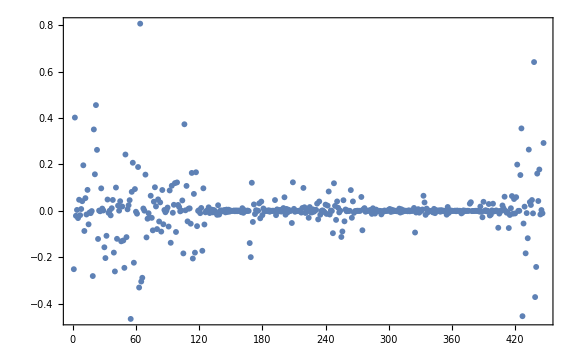
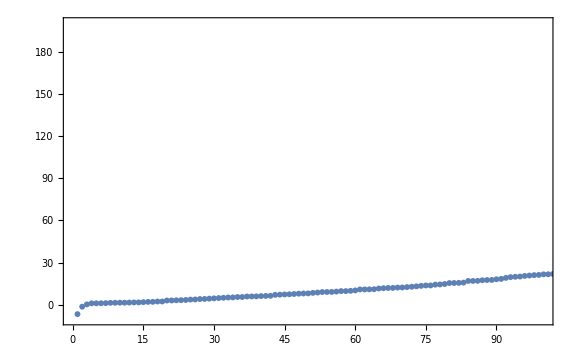
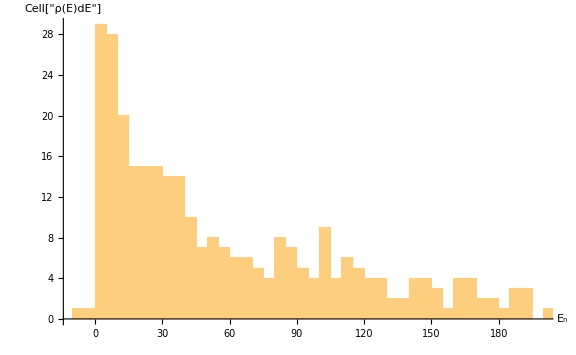
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
orderedEVSYHe3=Sort[Transpose[Eigensystem[tst=Transpose[He3Nmhi].He3Ham.He3Nmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{ei,v0t}=orderedEVSYHe3[[1]];

dE=5;
Print["B(^3He) = ",ei];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0t][[1]]]

fullv0=He3Nmhi.v0t;
Print["Norm=",fullv0.He3Norm.fullv0];
Grid[{{
ListPlot[Re[fullv0],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM basis vector}~n",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVSYHe3[[All,1]],PlotRange->{{0,100},{-10,200}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVSYHe3[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{"Cell[TextData[{\n\" \",\nCell[BoxData[FormBox[\nSubscriptBox[\"E\", \"n\"], TraditionalForm]]]\n}]]","Cell[\"ρ(E)dE\"]"}]
}}]
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(1/2)^- or J^π=(3/2)^- for the negative-parity rank-1 E_1 operator perturbing a helion;

```mathematica
matnames=FileNames["mat_*^-_BasNR-*"];
matnamesJ=Table[Select[matnames,StringMatchQ[#,"*"<>ToString[Subscript[I, n][[Inn]]]<>"*"]&],{Inn,Range[Length[Subscript[I, n]]]}];

LitNormHamMat=Table[readREAL8list[#]&/@Sort[matnamesJ[[Inn]],ToExpression[StringSplit[#1,"-"][[-1]]]<ToExpression[StringSplit[#2,"-"][[-1]]]&],{Inn,Range[Length[Subscript[I, n]]]}];

ActiveBasVFin=Table[Table[ReadList["Ssigbasv3heLIT_"<>ToString[Subscript[I, n][[Inn]]]<>"^-_BasNR-"<>ToString[nn]<>".dat"],{nn,Range[anzBas]-1}],{Inn,Range[Length[Subscript[I, n]]]}];

LITbasisDim=Table[IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat[[Inn]],{Inn,Range[Length[Subscript[I, n]]]}];

Print["N_(final - full) = ",LITbasisDim];
LitNorm=Table[ArrayReshape[LitNormHamMat[[Inn]][[#]][[1;;LITbasisDim[[Inn]][[#]]^2]],{LITbasisDim[[Inn]][[#]],LITbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
LitHam=Table[ArrayReshape[LitNormHamMat[[Inn]][[#]][[LITbasisDim[[Inn]][[#]]^2+1;;]],{LITbasisDim[[Inn]][[#]],LITbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];

Print["N_(final - active) = ",Length[#]&/@ActiveBasVFin];
Print["min/max Norm EV = ",Table[MinMax[Eigenvalues[LitNorm[[Inn]][[#]]]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}]];
```

N_(final - full) = {{201,175,190,197,189,209,210,165,213,200,207,247,235,183,188,205,193,191,249,216,208},{252,249,243,253,238,269,233,277,293,296,255,231,245,284,241,233,287,225,247,268,254}}

N_(final - active) = {21,21}

min/max Norm EV = {{{0.0000987591,10.2938},{0.0000115208,6.05574},{4.34857×10^-9,8.02898},{4.31064×10^-9,9.52763},{4.21039×10^-6,8.00395},{9.14644×10^-9,7.40103},{5.89273×10^-7,7.05902},{1.1091×10^-10,7.29307},{0.00001865,8.26183},{0.00232334,8.31489},{0.0000707299,10.0453},{2.48992×10^-7,10.9634},{1.09741×10^-6,14.087},{9.26502×10^-6,8.86524},{0.001085,9.67702},{9.911×10^-8,10.2764},{5.43253×10^-9,8.13151},{0.0000736273,8.91986},{9.85416×10^-9,12.3443},{0.000024095,10.6555},{0.0000628646,7.16833}},{{0.00444639,8.05631},{2.22727×10^-7,7.78228},{0.00217508,7.24258},{1.25806×10^-8,9.34674},{0.000033081,9.26066},{0.000756004,7.76755},{0.000543824,7.94712},{0.000729557,7.6705},{2.76693×10^-7,14.9912},{7.46224×10^-6,10.1299},{1.31964×10^-7,7.02006},{6.33883×10^-9,7.27666},{6.16159×10^-8,6.60321},{0.000835568,7.87244},{0.00184367,8.73054},{0.0002122,7.57744},{7.24192×10^-8,11.9484},{0.0000914175,8.45469},{2.69356×10^-6,6.89238},{8.32557×10^-8,9.66271},{2.8875×10^-11,8.38465}}}

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in RGM Basis

```mathematica
dE=2.;
plts={};
Do[
Do[
Print["=== I_n=",Subscript[I, n][[nj]],"  BasNR: ",nb," ==="];
Print["Final-state Basis dimension = ",Dimensions[LitNorm[[nj]][[nb]]]];
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]][[nb]],thresholdLIT];
orderedEVSYLIT=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]][[nb]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{eth,v0t}=orderedEVSYLIT[[1]];

v0l=LitNmhi.v0t;
Print["Norm=",v0l.LitNorm[[nj]][[nb]].v0l];
Print["lowest EV's: ",orderedEVSYLIT[[All,1]][[;;5]]];

plt1=ListPlot[Re[v0l],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large];

plt2=ListPlot[#[[1]]&/@orderedEVSYLIT,PlotRange->{{0,160},{-4,20}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large];
plt3=Histogram[#[[1]]&/@orderedEVSYLIT,{dE},ImageSize->Large,PlotRange->{{-10,100},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}];
AppendTo[plts,{plt1,plt2,plt3}];
Print["==="];
,{nb,Range[anzBas]}];
,{nj,Range[1,Length[Subscript[I, n]]]}];
```

=== I_n=0.5  BasNR: 1 ===

Final-state Basis dimension = {201,201}

min/max: {0.0000987591,10.2938}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.108485,0.13828,0.147602,0.202482,0.275727}

===

=== I_n=0.5  BasNR: 2 ===

Final-state Basis dimension = {175,175}

min/max: {0.0000115208,6.05574}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.060896,0.184477,0.252451,0.30705,0.333558}

===

=== I_n=0.5  BasNR: 3 ===

Final-state Basis dimension = {190,190}

min/max: {4.34857×10^-9,8.02898}

(min/max) discarded elements: 5 {4.34857×10^-9,4.09232×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.108947,0.21625,0.325174,0.333629,0.346589}

===

=== I_n=0.5  BasNR: 4 ===

Final-state Basis dimension = {197,197}

min/max: {4.31064×10^-9,9.52763}

(min/max) discarded elements: 3 {4.31064×10^-9,6.56232×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.220123,0.310965,0.336328,0.355625,0.400637}

===

=== I_n=0.5  BasNR: 5 ===

Final-state Basis dimension = {189,189}

min/max: {4.21039×10^-6,8.00395}

(min/max) discarded elements: 1 {4.21039×10^-6,4.21039×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0460551,0.098749,0.127849,0.143538,0.181896}

===

=== I_n=0.5  BasNR: 6 ===

Final-state Basis dimension = {209,209}

min/max: {9.14644×10^-9,7.40103}

(min/max) discarded elements: 1 {9.14644×10^-9,9.14644×10^-9}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.145649,0.262613,0.271688,0.358963,0.364305}

===

=== I_n=0.5  BasNR: 7 ===

Final-state Basis dimension = {210,210}

min/max: {5.89273×10^-7,7.05902}

(min/max) discarded elements: 3 {5.89273×10^-7,9.84978×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0602414,0.156493,0.177029,0.277033,0.335012}

===

=== I_n=0.5  BasNR: 8 ===

Final-state Basis dimension = {165,165}

min/max: {1.1091×10^-10,7.29307}

(min/max) discarded elements: 2 {1.1091×10^-10,6.82725×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.261945,0.275401,0.297669,0.331522,0.416332}

===

=== I_n=0.5  BasNR: 9 ===

Final-state Basis dimension = {213,213}

min/max: {0.00001865,8.26183}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0949557,0.185568,0.214771,0.229485,0.240064}

===

=== I_n=0.5  BasNR: 10 ===

Final-state Basis dimension = {200,200}

min/max: {0.00232334,8.31489}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0450936,0.0843153,0.100483,0.129712,0.292556}

===

=== I_n=0.5  BasNR: 11 ===

Final-state Basis dimension = {207,207}

min/max: {0.0000707299,10.0453}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.122688,0.160029,0.205114,0.214552,0.272421}

===

=== I_n=0.5  BasNR: 12 ===

Final-state Basis dimension = {247,247}

min/max: {2.48992×10^-7,10.9634}

(min/max) discarded elements: 3 {2.48992×10^-7,9.21485×10^-7}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0510051,0.129855,0.205479,0.219318,0.247285}

===

=== I_n=0.5  BasNR: 13 ===

Final-state Basis dimension = {235,235}

min/max: {1.09741×10^-6,14.087}

(min/max) discarded elements: 4 {1.09741×10^-6,3.78166×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.72412,-1.18904,-0.625066,0.187417,0.212088}

===

=== I_n=0.5  BasNR: 14 ===

Final-state Basis dimension = {183,183}

min/max: {9.26502×10^-6,8.86524}

(min/max) discarded elements: 1 {9.26502×10^-6,9.26502×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.068028,0.131887,0.192117,0.252033,0.313573}

===

=== I_n=0.5  BasNR: 15 ===

Final-state Basis dimension = {188,188}

min/max: {0.001085,9.67702}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.240109,0.247585,0.282842,0.303123,0.304076}

===

=== I_n=0.5  BasNR: 16 ===

Final-state Basis dimension = {205,205}

min/max: {9.911×10^-8,10.2764}

(min/max) discarded elements: 2 {9.911×10^-8,3.64515×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.138368,0.199527,0.226719,0.301887,0.344117}

===

=== I_n=0.5  BasNR: 17 ===

Final-state Basis dimension = {193,193}

min/max: {5.43253×10^-9,8.13151}

(min/max) discarded elements: 3 {5.43253×10^-9,3.71712×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.11383,0.123803,0.151975,0.217281,0.247562}

===

=== I_n=0.5  BasNR: 18 ===

Final-state Basis dimension = {191,191}

min/max: {0.0000736273,8.91986}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.103866,0.232078,0.239707,0.335191,0.439787}

===

=== I_n=0.5  BasNR: 19 ===

Final-state Basis dimension = {249,249}

min/max: {9.85416×10^-9,12.3443}

(min/max) discarded elements: 4 {9.85416×10^-9,2.47299×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.7387,-0.978055,-0.414407,0.100512,0.165447}

===

=== I_n=0.5  BasNR: 20 ===

Final-state Basis dimension = {216,216}

min/max: {0.000024095,10.6555}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.35564,-0.432821,0.0979798,0.154499,0.17948}

===

=== I_n=0.5  BasNR: 21 ===

Final-state Basis dimension = {208,208}

min/max: {0.0000628646,7.16833}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.041304,0.141784,0.15374,0.212504,0.246808}

===

=== I_n=1.5  BasNR: 1 ===

Final-state Basis dimension = {252,252}

min/max: {0.00444639,8.05631}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0772244,0.0886356,0.113801,0.140138,0.159416}

===

=== I_n=1.5  BasNR: 2 ===

Final-state Basis dimension = {249,249}

min/max: {2.22727×10^-7,7.78228}

(min/max) discarded elements: 6 {2.22727×10^-7,4.16097×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0909636,0.0950686,0.112697,0.135329,0.14344}

===

=== I_n=1.5  BasNR: 3 ===

Final-state Basis dimension = {243,243}

min/max: {0.00217508,7.24258}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0600111,0.0793764,0.103304,0.10667,0.10753}

===

=== I_n=1.5  BasNR: 4 ===

Final-state Basis dimension = {253,253}

min/max: {1.25806×10^-8,9.34674}

(min/max) discarded elements: 2 {1.25806×10^-8,3.74206×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0976932,0.110513,0.145642,0.215872,0.264147}

===

=== I_n=1.5  BasNR: 5 ===

Final-state Basis dimension = {238,238}

min/max: {0.000033081,9.26066}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0997239,0.142691,0.147554,0.15536,0.168478}

===

=== I_n=1.5  BasNR: 6 ===

Final-state Basis dimension = {269,269}

min/max: {0.000756004,7.76755}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0640953,0.0872423,0.107418,0.110172,0.112587}

===

=== I_n=1.5  BasNR: 7 ===

Final-state Basis dimension = {233,233}

min/max: {0.000543824,7.94712}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.132207,0.190322,0.191536,0.203475,0.223505}

===

=== I_n=1.5  BasNR: 8 ===

Final-state Basis dimension = {277,277}

min/max: {0.000729557,7.6705}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0350906,0.0693425,0.128677,0.161409,0.186663}

===

=== I_n=1.5  BasNR: 9 ===

Final-state Basis dimension = {293,293}

min/max: {2.76693×10^-7,14.9912}

(min/max) discarded elements: 6 {2.76693×10^-7,8.3813×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.72649,-1.11059,-0.477386,0.0680553,0.106091}

===

=== I_n=1.5  BasNR: 10 ===

Final-state Basis dimension = {296,296}

min/max: {7.46224×10^-6,10.1299}

(min/max) discarded elements: 1 {7.46224×10^-6,7.46224×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.6695,-0.890103,-0.561729,0.0717172,0.136261}

===

=== I_n=1.5  BasNR: 11 ===

Final-state Basis dimension = {255,255}

min/max: {1.31964×10^-7,7.02006}

(min/max) discarded elements: 2 {1.31964×10^-7,8.10998×10^-7}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0569116,0.0830469,0.107473,0.120885,0.177227}

===

=== I_n=1.5  BasNR: 12 ===

Final-state Basis dimension = {231,231}

min/max: {6.33883×10^-9,7.27666}

(min/max) discarded elements: 5 {6.33883×10^-9,7.49697×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0839104,0.100961,0.20349,0.24127,0.252315}

===

=== I_n=1.5  BasNR: 13 ===

Final-state Basis dimension = {245,245}

min/max: {6.16159×10^-8,6.60321}

(min/max) discarded elements: 2 {6.16159×10^-8,1.18759×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0970371,0.114512,0.137101,0.200561,0.24623}

===

=== I_n=1.5  BasNR: 14 ===

Final-state Basis dimension = {284,284}

min/max: {0.000835568,7.87244}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.67943,-1.26834,0.0833981,0.106415,0.130467}

===

=== I_n=1.5  BasNR: 15 ===

Final-state Basis dimension = {241,241}

min/max: {0.00184367,8.73054}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0815259,0.107185,0.109932,0.141113,0.149198}

===

=== I_n=1.5  BasNR: 16 ===

Final-state Basis dimension = {233,233}

min/max: {0.0002122,7.57744}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0694693,0.0897482,0.134675,0.151098,0.157214}

===

=== I_n=1.5  BasNR: 17 ===

Final-state Basis dimension = {287,287}

min/max: {7.24192×10^-8,11.9484}

(min/max) discarded elements: 2 {7.24192×10^-8,5.55894×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.20068,-0.76624,0.0116398,0.0659225,0.072623}

===

=== I_n=1.5  BasNR: 18 ===

Final-state Basis dimension = {225,225}

min/max: {0.0000914175,8.45469}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.182501,0.190628,0.24312,0.270879,0.27747}

===

=== I_n=1.5  BasNR: 19 ===

Final-state Basis dimension = {247,247}

min/max: {2.69356×10^-6,6.89238}

(min/max) discarded elements: 2 {2.69356×10^-6,8.75248×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0581687,0.105037,0.121631,0.128932,0.159322}

===

=== I_n=1.5  BasNR: 20 ===

Final-state Basis dimension = {268,268}

min/max: {8.32557×10^-8,9.66271}

(min/max) discarded elements: 5 {8.32557×10^-8,3.42529×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0508473,0.0831476,0.0868794,0.116993,0.127962}

===

=== I_n=1.5  BasNR: 21 ===

Final-state Basis dimension = {254,254}

min/max: {2.8875×10^-11,8.38465}

(min/max) discarded elements: 3 {2.8875×10^-11,2.34537×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.210607,0.233409,0.283512,0.29545,0.34503}

===

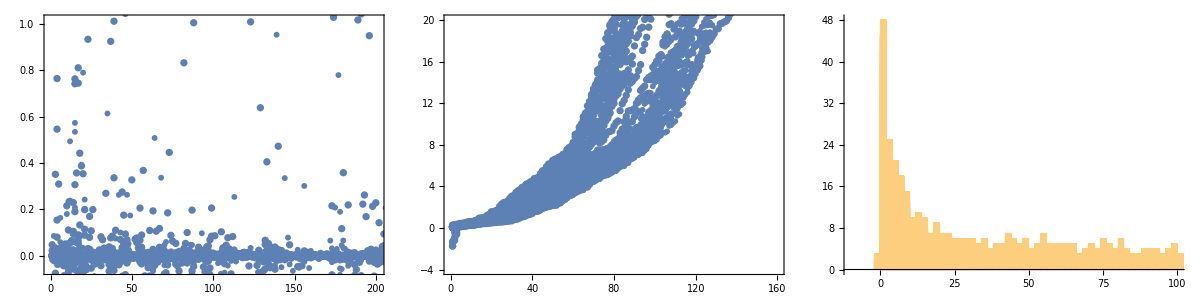

```mathematica
Grid[{{
Show[plts[[All,1]]],
Show[plts[[All,2]]],
Show[plts[[All,3]]]
}}]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

Normalise coupling blocks!!!!

```mathematica
CouplingBlockjs={};
CouplingBlockjAs={};

Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

CouplingBlockj={};
CouplingBlockjA={};

Do[

CouplingBlock={};
CouplingBlockT={};
CouplingBlockTA={};

Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];
	(*Why is mM unused here *)
fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"_BasNR-"<>ToString[nb-1]<>"."<>dt;
tmp =BinaryReadList[fntmp,datatype];

OutDim=Dimensions[tmp][[1]]/BareDims[[nb]][[1]];

test=ArrayReshape[tmp,{OutDim,BareDims[[nb]][[1]]}][[;;;;dH,;;;;dH]];
AppendTo[CouplingBlockT,{mIn,test}];
AppendTo[CouplingBlockTA,{mIn,test[[ActiveBasVFin[[nj]][[nb]],ActiveBasVHe3]]}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockj,CouplingBlockT];
AppendTo[CouplingBlockjA,CouplingBlockTA];

,{nb,Range[anzBas]}];

AppendTo[CouplingBlockjs,CouplingBlockj];
AppendTo[CouplingBlockjAs,CouplingBlockjA];

,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim_active(⟨ψ|ο̂|helion⟩) = ",Table[Dimensions[CouplingBlockjAs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];

Print["Dim_bare(⟨ψ|ο̂|helion⟩)   = ",Table[Dimensions[CouplingBlockjs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];

Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Table[Dimensions[LitHam[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Table[Dimensions[LitNorm[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
```

Dim_active(⟨ψ|ο̂|helion⟩) = {{{201,447},{175,447},{190,447},{197,447},{189,447},{209,447},{210,447},{165,447},{213,447},{200,447},{207,447},{247,447},{235,447},{183,447},{188,447},{205,447},{193,447},{191,447},{249,447},{216,447},{208,447}},{{252,447},{249,447},{243,447},{253,447},{238,447},{269,447},{233,447},{277,447},{293,447},{296,447},{255,447},{231,447},{245,447},{284,447},{241,447},{233,447},{287,447},{225,447},{247,447},{268,447},{254,447}}}

Dim_bare(⟨ψ|ο̂|helion⟩)   = {{{202,449},{175,449},{192,449},{197,449},{189,449},{209,449},{210,449},{168,449},{213,449},{200,449},{207,449},{247,449},{235,449},{183,449},{188,449},{205,449},{194,449},{191,449},{250,449},{216,449},{208,449}},{{255,449},{255,449},{243,449},{253,449},{238,449},{269,449},{233,449},{277,449},{293,449},{296,449},{255,449},{234,449},{245,449},{284,449},{241,449},{233,449},{287,449},{225,449},{247,449},{268,449},{254,449}}}

Dim(⟨ψ|Ĥ|ψ⟩) = {{{201,201},{175,175},{190,190},{197,197},{189,189},{209,209},{210,210},{165,165},{213,213},{200,200},{207,207},{247,247},{235,235},{183,183},{188,188},{205,205},{193,193},{191,191},{249,249},{216,216},{208,208}},{{252,252},{249,249},{243,243},{253,253},{238,238},{269,269},{233,233},{277,277},{293,293},{296,296},{255,255},{231,231},{245,245},{284,284},{241,241},{233,233},{287,287},{225,225},{247,247},{268,268},{254,254}}}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {{{201,201},{175,175},{190,190},{197,197},{189,189},{209,209},{210,210},{165,165},{213,213},{200,200},{207,207},{247,247},{235,235},{183,183},{188,188},{205,205},{193,193},{191,191},{249,249},{216,216},{208,208}},{{252,252},{249,249},{243,243},{253,253},{238,238},{269,269},{233,233},{277,277},{293,293},{296,296},{255,255},{231,231},{245,245},{284,284},{241,241},{233,233},{287,287},{225,225},{247,247},{268,268},{254,254}}}

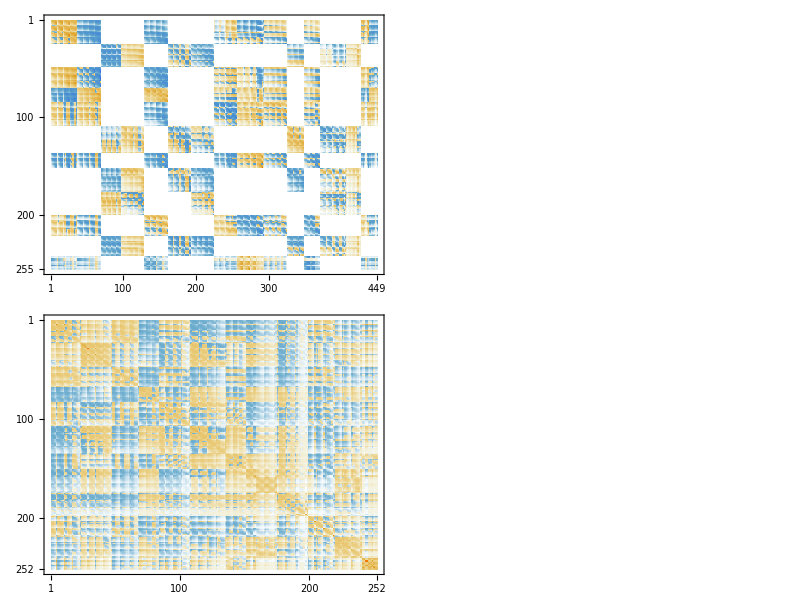

```mathematica
nb=1;nj=2;
Grid[{{
MatrixPlot[Chop[CouplingBlockjs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Coupling Matrix}",Magnification->2],ImageSize->Large]
,
MatrixPlot[Chop[CouplingBlockjAs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Optimal Coupling}",Magnification->2],ImageSize->Large]
},{
MatrixPlot[Chop[LitHam[[nj]][[nb]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Final-state Hamiltonian}",Magnification->2],ImageSize->Large]
,
MatrixPlot[Chop[He3Ham],FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Helion Hamiltonian}",Magnification->2],ImageSize->Large]
}}]
```

#### Analysis of RHS

```mathematica
OμRHSEB=normreg[thresholdLIT,He3Norm];
tmp=(Transpose[OμRHSEB].He3Ham).OμRHSEB; tmp=(tmp+Transpose[tmp])/2;
{λsHeEB,trfHeEB}=Eigensystem[tmp];
evgsEB=Flatten[trfHeEB[[TakeSmallest[λsHeEB->"Index",1]]]];
inhomoEB={};evgsEB=OμRHSEB.evgsEB;
Print["ev=",TakeSmallest[λsHeEB,1][[1]]," norm=",evgsEB.He3Norm.evgsEB];
```

ev=-6.60248 norm=1.

```mathematica
inhomoEB=Table[{},{nj,Length[Subscript[I, n]]}];
pltss={};
Do[
Do[
OμLHSEB=normreg[thresholdLIT,LitNorm[[nj]][[nb]]];
tmp=(Transpose[OμLHSEB].LitHam[[nj]][[nb]]).OμLHSEB;
tmp=(tmp+Transpose[tmp])/2;
{λfinalEB,trfLitEB}=Eigensystem[tmp];
Do[
tmp=CouplingBlockjAs[[nj]][[nb]][[mm]][[2]];
AppendTo[inhomoEB[[nj]],Transpose[OμLHSEB].(tmp.evgsEB)];
,{mm,Range[1,Length[mIns[[nj]]]]}
];AppendTo[pltss,ListPlot[inhomoEB[[nj]],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert O\\Big\\vert \\text{He}3 \\right\\rangle",Magnification->2]},ImageSize->Large]];
,{nb,Range[anzBas]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
];
Show[pltss]
```

-Graphics-

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

```mathematica
lpsisEV={};CumStrengthsEV={};

{μEV,transfEV}=Transpose[Select[Sort[Transpose[Eigensystem[He3Norm]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμRHSEV=(Transpose[transfEV].DiagonalMatrix[μEV^(-1/2)]);

{EvalsIEV,EvecsIEV}=Eigensystem[tmp=(Transpose[OμRHSEV].He3Ham).OμRHSEV;(tmp+Transpose[tmp])/2];
EvecGSiEV=OμRHSEV.Flatten[EvecsIEV[[TakeSmallest[EvalsIEV->"Index",1]]]];
EvalGSiEV=Min[EvalsIEV];
EvalGSiEV
{EvecGSiEV.He3Norm.EvecGSiEV,EvecGSiEV.He3Ham.EvecGSiEV}
```

-6.60248

{1.,-6.60248}

```mathematica
CumStrengthsJ={};pltsssJ={};
Do[
CumStrengths={};pltsss={};
Print[" J_final = ",Subscript[I, n][[nj]]];
Print["E_0^initial = ",EvalGSiEV,"    dim = ",Dimensions[EvalsIEV]];
Do[

{μlEV,transflEV}=Transpose[Select[Sort[Transpose[Eigensystem[LitNorm[[nj]][[nb]]]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμLHSEV=(Transpose[transflEV].DiagonalMatrix[μlEV^(-1/2)]);

{EvalsFEV,EvecsFEV}=Eigensystem[tmp=(Transpose[OμLHSEV].(LitHam[[nj]][[nb]])).OμLHSEV;(tmp+Transpose[tmp])/2];
{EvalsFEV,EvecsFEV}=Sort[{EvalsFEV,EvecsFEV},#1[[1]]<#2[[1]]&];
EvecGSfEV=OμLHSEV.Flatten[EvecsFEV[[TakeSmallest[EvalsFEV->"Index",1]]]];
EvalGSfEV=Min[EvalsFEV];


Print["Basisensemble ",nb,":  E_0^final  = ",EvalGSfEV,"    dim   = ",Dimensions[EvalsFEV]];
tmplEV=0;

Do[
inhomoEV=Transpose[OμLHSEV].(CouplingBlockjAs[[nj]][[nb]][[mm]][[2]].EvecGSiEV);

tmplEV=tmplEV+(EvecsFEV.inhomoEV)^2;
,{mm,Length[mIns[[nj]]]}
];
lpsisEV=Transpose[{EvalsFEV,tmplEV}];

CumStrengthsEV=Transpose[{Sort[lpsisEV][[All,1]],Accumulate[Sort[lpsisEV][[All,2]]]}];

pl1=
ListPlot[lpsisEV,Joined->False,PlotMarkers->{{♔,12},{♗,12}},PlotRange->{{-3,7.5},{0,Automatic}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{Full,Full},AxesLabel->{MaTeX["\\text{E~[MeV]}",Magnification->2],MaTeX["\\left\\langle J^\\pi_{E_n=\\omega_\\text{lab}-E_0}\\Big\\vert\\widehat{E1}\\Big\\vert\\left({}^3\\text{He}\\right)_{E_0}^{1/2^+}\\right\\rangle^2",Magnification->2]},ImageSize->ImgSize];
pl2=
ListPlot[CumStrengthsEV,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,350},{0,Automatic}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2]];

AppendTo[pltsss,{pl1,pl2}];
AppendTo[CumStrengths,CumStrengthsEV];

,{nb,Range[anzBas]}
];
AppendTo[pltsssJ,pltsss];
AppendTo[CumStrengthsJ,CumStrengths];
,{nj,Range[1,Length[Subscript[I, n]]]}
]
```

J_final = 0.5

E_0^initial = -6.60248    dim = {439}

Basisensemble 1:  E_0^final  = 0.108485    dim   = {201}

Basisensemble 2:  E_0^final  = 0.060896    dim   = {175}

Basisensemble 3:  E_0^final  = 0.108947    dim   = {185}

Basisensemble 4:  E_0^final  = 0.220123    dim   = {194}

Basisensemble 5:  E_0^final  = 0.0460551    dim   = {188}

Basisensemble 6:  E_0^final  = 0.145649    dim   = {208}

Basisensemble 7:  E_0^final  = 0.0602414    dim   = {207}

Basisensemble 8:  E_0^final  = 0.261945    dim   = {163}

Basisensemble 9:  E_0^final  = 0.0949557    dim   = {213}

Basisensemble 10:  E_0^final  = 0.0450936    dim   = {200}

Basisensemble 11:  E_0^final  = 0.122688    dim   = {207}

Basisensemble 12:  E_0^final  = 0.0510051    dim   = {244}

Basisensemble 13:  E_0^final  = -1.72412    dim   = {231}

Basisensemble 14:  E_0^final  = 0.068028    dim   = {182}

Basisensemble 15:  E_0^final  = 0.240109    dim   = {188}

Basisensemble 16:  E_0^final  = 0.138368    dim   = {203}

Basisensemble 17:  E_0^final  = 0.11383    dim   = {190}

Basisensemble 18:  E_0^final  = 0.103866    dim   = {191}

Basisensemble 19:  E_0^final  = -1.7387    dim   = {245}

Basisensemble 20:  E_0^final  = -1.35564    dim   = {216}

Basisensemble 21:  E_0^final  = 0.041304    dim   = {208}

J_final = 1.5

E_0^initial = -6.60248    dim = {439}

Basisensemble 1:  E_0^final  = 0.0772244    dim   = {252}

Basisensemble 2:  E_0^final  = 0.0909636    dim   = {243}

Basisensemble 3:  E_0^final  = 0.0600111    dim   = {243}

Basisensemble 4:  E_0^final  = 0.0976932    dim   = {251}

Basisensemble 5:  E_0^final  = 0.0997239    dim   = {238}

Basisensemble 6:  E_0^final  = 0.0640953    dim   = {269}

Basisensemble 7:  E_0^final  = 0.132207    dim   = {233}

Basisensemble 8:  E_0^final  = 0.0350906    dim   = {277}

Basisensemble 9:  E_0^final  = -1.72649    dim   = {287}

Basisensemble 10:  E_0^final  = -1.6695    dim   = {295}

Basisensemble 11:  E_0^final  = 0.0569116    dim   = {253}

Basisensemble 12:  E_0^final  = 0.0839104    dim   = {226}

Basisensemble 13:  E_0^final  = 0.0970371    dim   = {243}

Basisensemble 14:  E_0^final  = -1.67943    dim   = {284}

Basisensemble 15:  E_0^final  = 0.0815259    dim   = {241}

Basisensemble 16:  E_0^final  = 0.0694693    dim   = {233}

Basisensemble 17:  E_0^final  = -1.20068    dim   = {285}

Basisensemble 18:  E_0^final  = 0.182501    dim   = {225}

Basisensemble 19:  E_0^final  = 0.0581687    dim   = {245}

Basisensemble 20:  E_0^final  = 0.0508473    dim   = {263}

Basisensemble 21:  E_0^final  = 0.210607    dim   = {251}

```mathematica
Dimensions[CumStrengthsJ[[1]][[{1,3,4}]]]
```

{3}

```mathematica
Integrate[8 Pi^2 x^2 (x Exp[-x^2/(4 α)-(ω-0.75 x^2)/α]/(3 Pi^1.5 α^2.5))^2/(2 √(ω-0.75 x^2)),{x,0,√(4. ω/3.)},Assumptions->{α∈Reals,α>0,ω∈Reals,ω>0}];

NielsF[ω_,α_]:=(ⅇ^(-(4 ω)/(3 α)) ((ω/α)^2 BesselI[0,(2 ω)/(3 α)]+((ω/α)^2-3 ω/α) BesselI[1,(2 ω)/(3 α)]))/(81 √3 α^2);
NielsC[λ_,α_]:=NIntegrate[NielsF[ω,α],{ω,0,λ}]

emin=-3;emax=1250;
sc=0.975 (4 Pi/137)^-1;
αRGM=1.8;

CumStrengthsJwithD={};
FittedCum={};FittedCum2={};
StrengthF={};StrengthF2={};
mn=0.000001;

basIndices=Range[anzBas];

Do[
Clear[a,b,c,a2,b2,c2,d2];
cleanSet=Flatten[Select[Sort[CumStrengthsJ[[nj]][[basIndices]]],#[[1]][[1]]>-10&],1];
offset=Min[cleanSet[[All,1]]];
fitSetShifted=Chop[Transpose[{cleanSet[[All,1]]-offset,cleanSet[[All,2]]}]];
ffun=(b(x+mn)^a)/(1+c(x+mn)^a);
ffun2=(b2(x+mn)^a2)/(1+d2(x+mn)^(a2/2)+c2(x+mn)^a2);
rr=FindFit[fitSetShifted,ffun,{a,b,c},x];
rr2=FindFit[fitSetShifted,ffun2,{a2,b2,c2,d2},x];
AppendTo[CumStrengthsJwithD,cleanSet];
AppendTo[FittedCum,ffun/.rr/.x->e-offset];
AppendTo[StrengthF,D[FittedCum[[-1]],e]];
AppendTo[FittedCum2,ffun2/.rr2/.x->e-offset];
AppendTo[StrengthF2,D[FittedCum2[[-1]],e]];
,{nj,Range[Length[Subscript[I, n]]]}];
plott=Show[
ListPlot[CumStrengthsJwithD[[2]],Joined->False,ImageSize->ImgSize,PlotRange->{{emin,emax},Full},AxesLabel->{MaTeX["\\epsilon_n=\\epsilon_i+\\omega~\\left[\\text{MeV}\\right]",Magnification->1],MaTeX["\\int_{-\\infty}^{\\epsilon_n}F\\left(\\epsilon_n\\right)",Magnification->1]},PlotLabel->MaTeX["\\epsilon_i^\\text{v18}\\approx-6.8~\\text{MeV}",Magnification->2],ImageSize->Large,PlotStyle->Directive[Blue,PointSize[0.005]],PlotLegends->MaTeX["\\color{blue}{J^\\pi=\\frac{3}{2}^-}",Magnification->1]],
ListPlot[CumStrengthsJwithD[[1]],Joined->False,ImageSize->ImgSize,PlotRange->{{emin,emax},Full},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->1],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->1]},PlotLabel->MaTeX["",Magnification->2],ImageSize->Large,PlotStyle->Directive[Black,PointSize[0.005]],PlotLegends->MaTeX["J^\\pi=\\frac{1}{2}^-",Magnification->1]],
Plot[FittedCum,{e,emin,emax},PlotRange->All,PlotStyle->{{Red,Dashed,Thickness[0.005]},{Green,Dotted,Thickness[0.005]}}],Plot[FittedCum2,{e,emin,emax},PlotRange->All,PlotStyle->{{Black,Thickness[0.0025]},{White,Thickness[0.0025]}}]
,ImageSize->ImgSize];
Export[resultsDir<>"/tmp.pdf",plott];
(*,
Plot[sc NielsC[λ/hbarsqO2m,αRGM]/fl,{λ,emin,emax},PlotRange->{{emin,emax},Automatic},PlotStyle->{Magenta,Thick},ImageSize->Large]*)

Put[CumStrengthsJwithD,LocalObject["CumStr_05_15"]]
```

LocalObject[file:///home/kirscher/.Wolfram/Objects/CumStr_05_15]

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

dipole calculation from B. Gibson & D.R. Lehmann, PRC 13,2 (1976) (T=3/2 only!)
and Golak et al.

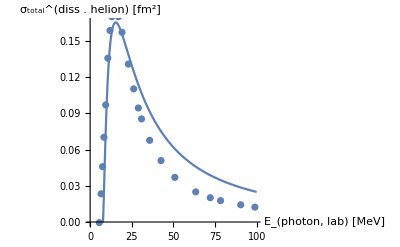

```mathematica
He3DatamBarnGolak=Import["../../data/he3_photo_diss_sigma_golak.dat","Data"];
He3DatamBarnGibson=Import["../../data/he3_photo_diss_sigma_gibson.dat","Data"];Bhe=7.67;
He3DataFm2=Transpose[{Transpose[He3DatamBarnGolak][[1]],Transpose[He3DatamBarnGolak][[2]] 10.^(-1)}];

σBethe[ω_,E0_,mM_]:=4 (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
Plot[hbarc^2 σBethe[ν,Bhe,938.],{ν,0,100},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . helion) [fm^2]"}],
ListPlot[He3DataFm2,PlotLabel->Style["Gibson - E1",Orange,22]]]
```

#### σ_tot=(2π)^2 α·E_γ ∑_(J,M) JM OverHat[E1](J_0 m_0)^2

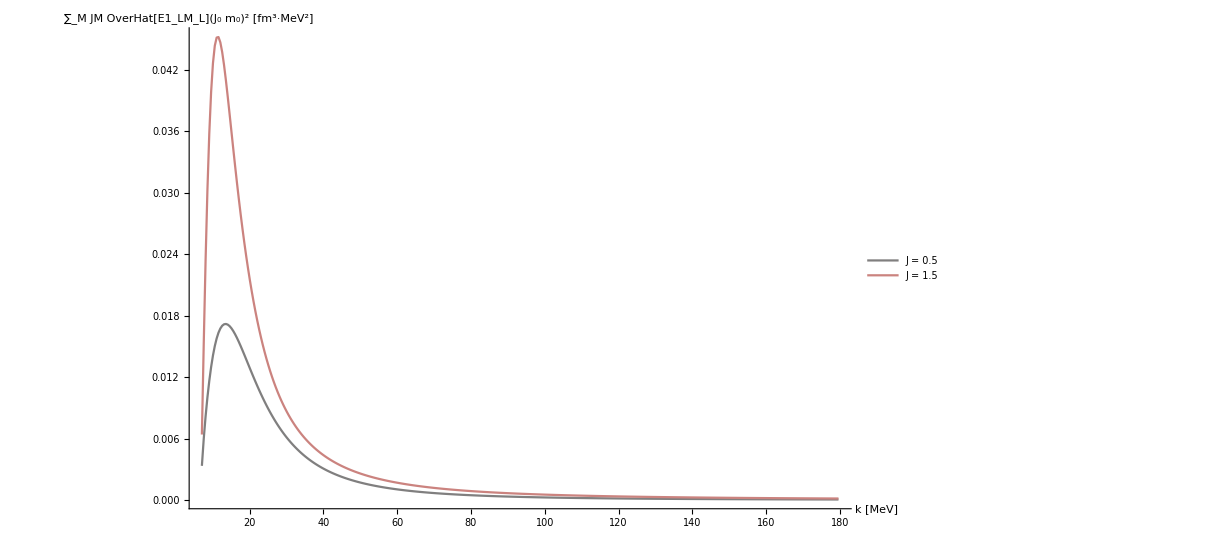
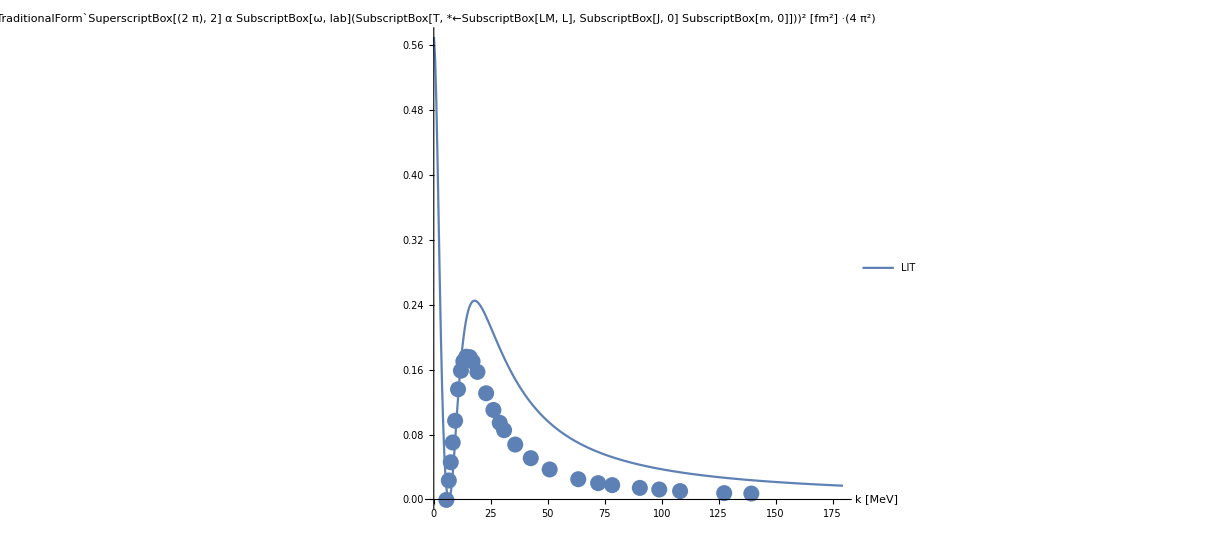
-Graphics- | -Graphics-

```mathematica
Clear[ee,e2];
k0=0.001;k1=180;dK=0.5;
Subscript[k, lab]=Range[Abs[eth],k1,dK];
Ji=Jf=J0;Mi=Ji;Mf=Mi;

labelj=("J = "<>ToString[#])&/@Subscript[I, n];

strengthfunctionList=Table[Table[(StrengthF2[[nJ]]/.e->ee)/.ee->(ei+kmag),{kmag,Subscript[k, lab]}],{nJ,Range[1,Length[Subscript[I, n]]]}];

z=List[];

For[nJ=1,nJ≤Length[Subscript[I, n]],nJ++,(
atmp=ListLinePlot[strengthfunctionList[[nJ,All]],PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","FormBox[RowBox[{UnderscriptBox[\"∑\", \"M\"], RowBox[{TemplateBox[{\"JM\"},\"Bra\"], OverscriptBox[SubscriptBox[\"E1\", SubscriptBox[\"LM\", \"L\"]], \"^\"], SuperscriptBox[TemplateBox[{RowBox[{SubscriptBox[\"J\", \"0\"], SubscriptBox[\"m\", \"0\"]}]},\"Ket\"], \"2\"]}]}],TraditionalForm] [fm^3·MeV^2]"},ImageSize->ImgSize,Joined->True,DataRange->{Min[Subscript[k, lab]],Max[Subscript[k, lab]]},PlotStyle->{ColorData[7,"ColorList"][[nJ]]},PlotLegends->{labelj[[nJ]]}];
AppendTo[z,atmp];
)];

Tsquared[Mf_,Mi_,λf_,θ_]:=
Module[{compo},
ampli=0;
For[nJ=1,nJ≤Length[Subscript[I, n]],nJ++,
compo=strengthfunctionList[[nJ,All]];
For[Mm=-multipolarity,Mm≤multipolarity,Mm++,
For[Mmp=-multipolarity,Mmp≤multipolarity,Mmp++,
ampli+=compo;
];
];];
Return[ampli]
]
fudgi=(2 π)^2;

kinfac=fudgi (2 Pi)^2 αfine (Subscript[k, lab]+ei)/hbarc;

DissCross[Mf_,Mi_,λf_,kinfac_]:=kinfac Tsquared[Mf,Mi,λf,θ];
lf=1;

Grid[{{
Show[z,PlotRange->All],
Show[ListPlot[Re[DissCross[Jf,Ji,lf,kinfac]],PlotRange->{Automatic,{0,Full}},LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`SuperscriptBox[(2  π), 2] α SubscriptBox[ω, lab](SubscriptBox[T, *←SubscriptBox[LM, L], SubscriptBox[J, 0] SubscriptBox[m, 0]]))^2 [fm^2] ·("<>ToString[Style[fudgi,Red],TraditionalForm]<>")"}(*,Filling->cycl*),ImageSize->ImgSize,Joined->{True,False},DataRange->{Min[Subscript[k, lab]],Max[Subscript[k, lab]]},PlotLegends->{"LIT"}],ListPlot[He3DataFm2,PlotLegends->"σ_tot data"]
]
}}]
```

d^5 σ_(He→npp)=(2π)^2 α ω_lab ∑|p_1 q_1Ô(ω)He|^2 d^3(p_1,q_1)δ(p_1^2+3/4 q_1^2-ω)

```mathematica
Clear[solu,wcm,wlab,wcem]
solu=Solve[wcm==wlab (1+2 wlab/mdeu)^(-1/2),wlab];
wl=Simplify[wlab/.solu[[2]]]

kcross=0.5 Sqrt[(wcem+e0-2 mn)(wcem+e0+2 mn)]
```

(wcm^2+√(wcm^2 (mdeu^2+wcm^2)))/mdeu

0.5 √((-2.×10^-6+e0+wcem) (2.×10^-6+e0+wcem))